{0.0003125,0.00035,0.0004,0.0004875,0.000575,0.000725,0.0009125,0.00125,0.0019,0.0032,0.00395,0.00365,0.0023,0.00155,0.00115,0.0009125,0.00075,0.0006375,0.0005625,0.0004875,0.0004375,0.0004125}

{0.0003,0.00035,0.000391667,0.000475,0.000566667,0.0007,0.000883333,0.00118333,0.0017,0.0025,0.00283333,0.00275,0.00206667,0.0015,0.00113333,0.0009,0.00075,0.00065,0.000575,0.000516667,0.000458333,0.000416667}

0.00279307

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {15.5334} lies outside the range of data in the interpolating function. Extrapolation will be used.

{x→4.73941}

0.00287512

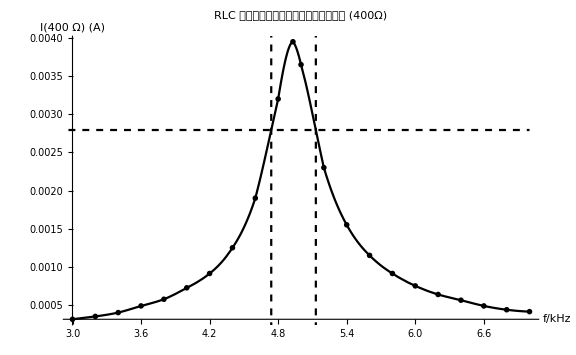

```mathematica
f = {3.0, 3.2, 3.4, 3.6, 3.8, 4.0, 4.2, 4.4, 4.6, 4.8, 4.92933, 5.0, 5.2, 5.4, 5.6, 5.8, 6.0, 6.2, 6.4, 6.6, 6.8, 7.0};

(* R = 400 *)
vrpp400 = {0.125, 0.140, 0.160, 0.195, 0.230, 0.290, 0.365, 0.500, 0.760, 1.280, 1.580, 1.460, 0.920, 0.620, 0.460, 0.365, 0.300, 0.255, 0.225, 0.195, 0.175, 0.165};
irpp400 = vrpp400 / 400

(* R = 600 *)
vrpp600 = {0.180, 0.210, 0.235, 0.285, 0.340, 0.420, 0.530, 0.710, 1.020, 1.500, 1.700, 1.650, 1.240, 0.900, 0.680, 0.540, 0.450, 0.390, 0.345, 0.310, 0.275, 0.250};
irpp600 = vrpp600 / 600

(* Draw R = 400 *)
data400 = Transpose[{f, irpp400}];
imax400 = Max[irpp400];
lessimax400 = imax400 / Sqrt[2]

(* Trying to find point *)
curve400 = Interpolation[data400, InterpolationOrder->3]
FindRoot[curve400[x] - lessimax400, {x, 3}]
curve400[5.11841]
Show[Plot[curve400[x],{x,3.0, 7.0}, PlotStyle->Black],
ListPlot[data400, PlotStyle->Black, PlotMarkers->{Style["X", 10]}],
Plot[lessimax400, {x, 0, 7.0}, PlotStyle->{Black, Dashed}], 
ContourPlot[x==5.129811181229793,{x,3,7},{y,0,0.005}, ContourStyle->{Black,Dashed}],
ContourPlot[x == 4.739410629105007, {x, 3, 7}, {y, 0, 0.005}, ContourStyle->{Black, Dashed}],
AxesLabel->{Style["f/kHz", 10, Bold], Style["I(400 Ω) (A)"]},
PlotLabel->Style["RLC 串联谐振电路总电流的幅频特性曲线 (400Ω)",15,FontFamily-> "Hack", Bold],
ImageSize->Large]

(* Draw R = 600 *)
data600 = Transpose[{f, irpp600}];
imax600 = Max[irpp600];
lessimax600 = imax600 / Sqrt[2]

(* Trying to find point *)
curve600 = Interpolation[data600, InterpolationOrder->3]
FindRoot[curve600[x] - lessimax600, {x, 5}]
curve600[5.11841]
Show[Plot[curve600[x],{x,3.0, 7.0}, PlotStyle->Black],
ListPlot[data600, PlotStyle->Black, PlotMarkers->{Style["X", 10]}],
Plot[lessimax600, {x, 0, 7.0}, PlotStyle->{Black, Dashed}], 
ContourPlot[x==5.219969939018847,{x,3,7},{y,0,0.005}, ContourStyle->{Black,Dashed}],
ContourPlot[x == 4.674611908118245, {x, 3, 7}, {y, 0, 0.005}, ContourStyle->{Black, Dashed}],
AxesLabel->{Style["f/kHz", 10, Bold], Style["I(600 Ω) (A)"]},
PlotLabel->Style["RLC 串联谐振电路总电流的幅频特性曲线 (600 Ω)",15,FontFamily-> "Hack", Bold],
ImageSize->Large]
```

```mathematica
Export["/Users/bbn/My/Git/PhyExam/2018-exp5/400Ohm.jpg",%264,"JPEG",ImageResolution->500]
```

/Users/bbn/My/Git/PhyExam/2018-exp5/400Ohm.jpg

```mathematica
Export["/Users/bbn/My/Git/PhyExam/2018-exp5/600Ohm.jpg",%271,"JPEG",ImageResolution->500]
```

/Users/bbn/My/Git/PhyExam/2018-exp5/600Ohm.jpg

/Users/bbn/My/Git/PhyExam/2018-exp5/600Ohm.jpg

/Users/bbn/My/Git/PhyExam/2018-exp5/400Ohm.jpg